```mathematica
filenames=FileNames["*jpeg",FileNameJoin[{NotebookDirectory[],"art-thumbnails"}]];
```

```mathematica
Length[filenames]
```

190

```mathematica
StringRiffle[Map[StringTemplate["'`1`'"],filenames],"\n"]//CopyToClipboard
```

```mathematica
Map[Export[#,Thumbnail[Import[#]]]&,filenames]
```

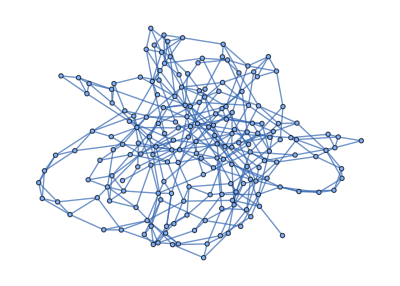

```mathematica
RandomGraph[WattsStrogatzGraphDistribution[190,.3]]
```

```mathematica
Length[Sort[Map[StringDelete[#,{DirectoryName[#],".png",".jpg",".jpeg",".JPG",".JPEG",".PNG",".webp"}]&,filenames]]]
```

183

```mathematica
edgeRules=AssociationThread[Sort[Map[StringDelete[#,{DirectoryName[#],".png",".jpg",".jpeg",".JPG",".JPEG",".PNG",".webp"}]&,filenames]]->#]&@(List@@@EdgeList[])
```

AssociationThread::idim: {0-Arango_Franco_Sara-CiudadBolivar,0-Arango_Franco_Sara-CiudadBolivarwindow_2aE,0-Arango_Franco_Sara-DedosDeMujerVanidosa,0-Arango_Franco_Sara-Flower1,0-Arango_Franco_Sara-Flowers,«41»,0-Arango_Franco_Sara-window_7,0-Arango_Franco_Sara-window_7E,0-Arango_Franco_Sara-window_8,0-Arango_Franco_Sara-window_9,«133»} and {{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{60,9},{9,10},{10,33},{80,12},{12,13},{5,14},{14,150},{15,16},{16,17},{17,18},{18,19},{188,20},{20,21},{21,22},«9»,{31,32},{32,33},{33,34},{34,35},{35,36},{36,37},{37,38},{38,39},{39,40},{40,41},{41,9},{42,43},{43,44},{44,55},{45,46},{46,47},{140,48},{147,49},{49,50},{50,44},«330»} must have the same length.

AssociationThread[{0-Arango_Franco_Sara-CiudadBolivar,0-Arango_Franco_Sara-CiudadBolivarwindow_2aE,0-Arango_Franco_Sara-DedosDeMujerVanidosa,0-Arango_Franco_Sara-Flower1,0-Arango_Franco_Sara-Flowers,0-Arango_Franco_Sara-garabatos,0-Arango_Franco_Sara-shapes,0-Arango_Franco_Sara-Teusaquillo,0-Arango_Franco_Sara-window_1,0-Arango_Franco_Sara-window_10,0-Arango_Franco_Sara-window_11,0-Arango_Franco_Sara-window_12,0-Arango_Franco_Sara-window_13,0-Arango_Franco_Sara-window_14,0-Arango_Franco_Sara-window_15,0-Arango_Franco_Sara-window_16,0-Arango_Franco_Sara-window_17,0-Arango_Franco_Sara-window_18,0-Arango_Franco_Sara-window_19,0-Arango_Franco_Sara-window_1E,0-Arango_Franco_Sara-window_2,0-Arango_Franco_Sara-window_20,0-Arango_Franco_Sara-window_21,0-Arango_Franco_Sara-window_22,0-Arango_Franco_Sara-window_23,0-Arango_Franco_Sara-window_24,0-Arango_Franco_Sara-window_25,0-Arango_Franco_Sara-window_26,0-Arango_Franco_Sara-window_27,0-Arango_Franco_Sara-window_28,0-Arango_Franco_Sara-window_29,0-Arango_Franco_Sara-window_2bE,0-Arango_Franco_Sara-window_3,0-Arango_Franco_Sara-window_30,0-Arango_Franco_Sara-window_31,0-Arango_Franco_Sara-window_32,0-Arango_Franco_Sara-window_33,0-Arango_Franco_Sara-window_3aE,0-Arango_Franco_Sara-window_3bE,0-Arango_Franco_Sara-window_4,0-Arango_Franco_Sara-window_4E,0-Arango_Franco_Sara-window_5,0-Arango_Franco_Sara-window_5aE,0-Arango_Franco_Sara-window_5B,0-Arango_Franco_Sara-window_6,0-Arango_Franco_Sara-window_6E,0-Arango_Franco_Sara-window_7,0-Arango_Franco_Sara-window_7E,0-Arango_Franco_Sara-window_8,0-Arango_Franco_Sara-window_9,0-Bulla_Lina-10,0-Bulla_Lina-2,0-Bulla_Lina-3,0-Bulla_Lina-4,0-Bulla_Lina-6,0-Bulla_Lina-7,0-Bulla_Lina-8,0-Bulla_Lina-9,0-Bulla_Lina-Flowers,0-Bulla_Lina-Moon_in_the_window,0-Camacho_Cabrera_Gabriel-1,0-Camacho_Cabrera_Gabriel-10,0-Camacho_Cabrera_Gabriel-2,0-Camacho_Cabrera_Gabriel-3,0-Camacho_Cabrera_Gabriel-4,0-Camacho_Cabrera_Gabriel-5,0-Camacho_Cabrera_Gabriel-6,0-Camacho_Cabrera_Gabriel-7,0-Camacho_Cabrera_Gabriel-8,0-Camacho_Cabrera_Gabriel-9,0-elly-androids dream,0-elly-bead_tests,0-elly-black_box_form,0-elly-cycles,0-elly-dripping_dry,0-elly-essence_of_shell,0-elly-flaked_brain,0-elly-foghorn_leghorn,0-elly-grid144,0-elly-high_dive,0-elly-kusama_digital_study,0-elly-likes_for_an_egg,0-elly-oh_its_you,0-elly-olfactory,0-elly-rule 110 difference,0-elly-sassafras,0-elly-scan_of_middle_aged_woman,0-elly-scan_of_young_woman,0-elly-september_cove,0-elly-storm_effects,0-elly-wrestlerblender,0-elly-yellow night,0-Emerson_Paquette-1,0-Emerson_Paquette-10,0-Emerson_Paquette-2,0-Emerson_Paquette-3,0-Emerson_Paquette-4,0-Emerson_Paquette-5,0-Emerson_Paquette-6,0-Emerson_Paquette-7,0-Emerson_Paquette-8,0-Emerson_Paquette-9,0-Louison_Halgand-1,0-Louison_Halgand-10,0-Louison_Halgand-11,0-Louison_Halgand-2,0-Louison_Halgand-3,0-Louison_Halgand-4,0-Louison_Halgand-5,0-Louison_Halgand-6,0-Louison_Halgand-7,0-Louison_Halgand-8,0-Louison_Halgand-9,0-Nadine_AbdElRazek-1,0-Nadine_AbdElRazek-10,0-Nadine_AbdElRazek-11,0-Nadine_AbdElRazek-12,0-Nadine_AbdElRazek-13,0-Nadine_AbdElRazek-2,0-Nadine_AbdElRazek-3,0-Nadine_AbdElRazek-4,0-Nadine_AbdElRazek-5,0-Nadine_AbdElRazek-6,0-Nadine_AbdElRazek-7,0-Nadine_AbdElRazek-8,0-Nadine_AbdElRazek-9,0-Phileas_Dazeley_Gaist-1,0-Phileas_Dazeley_Gaist-10,0-Phileas_Dazeley_Gaist-11,0-Phileas_Dazeley_Gaist-12,0-Phileas_Dazeley_Gaist-13,0-Phileas_Dazeley_Gaist-14,0-Phileas_Dazeley_Gaist-15,0-Phileas_Dazeley_Gaist-16,0-Phileas_Dazeley_Gaist-17,0-Phileas_Dazeley_Gaist-18,0-Phileas_Dazeley_Gaist-19,0-Phileas_Dazeley_Gaist-2,0-Phileas_Dazeley_Gaist-20,0-Phileas_Dazeley_Gaist-21,0-Phileas_Dazeley_Gaist-22,0-Phileas_Dazeley_Gaist-23,0-Phileas_Dazeley_Gaist-24,0-Phileas_Dazeley_Gaist-25,0-Phileas_Dazeley_Gaist-26,0-Phileas_Dazeley_Gaist-27,0-Phileas_Dazeley_Gaist-28,0-Phileas_Dazeley_Gaist-29,0-Phileas_Dazeley_Gaist-3,0-Phileas_Dazeley_Gaist-30,0-Phileas_Dazeley_Gaist-31,0-Phileas_Dazeley_Gaist-32,0-Phileas_Dazeley_Gaist-33,0-Phileas_Dazeley_Gaist-34,0-Phileas_Dazeley_Gaist-35,0-Phileas_Dazeley_Gaist-36,0-Phileas_Dazeley_Gaist-37,0-Phileas_Dazeley_Gaist-4,0-Phileas_Dazeley_Gaist-5,0-Phileas_Dazeley_Gaist-6,0-Phileas_Dazeley_Gaist-7,0-Phileas_Dazeley_Gaist-8,0-Phileas_Dazeley_Gaist-9,0-Sonal_Raghuvanshi-1,0-Sonal_Raghuvanshi-10,0-Sonal_Raghuvanshi-2,0-Sonal_Raghuvanshi-3,0-Sonal_Raghuvanshi-4,0-Sonal_Raghuvanshi-5,0-Sonal_Raghuvanshi-6,0-Sonal_Raghuvanshi-7,0-Sonal_Raghuvanshi-8,0-Sonal_Raghuvanshi-9,0-Thompson_Kyle-Beauty_Haiku,0-Thompson_Kyle-Butterfly,0-Thompson_Kyle-Earth_Haiku,0-Thompson_Kyle-Moon_Haiku,0-Thompson_Kyle-Morning_Haiku,0-Thompson_Kyle-Orange_Flowers,0-Thompson_Kyle-Purple_Flowers,0-Thompson_Kyle-Sunflower_Poem,0-Thompson_Kyle-Sunflowers,0-Thompson_Kyle-Sun_Haiku}→{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{60,9},{9,10},{10,33},{80,12},{12,13},{5,14},{14,150},{15,16},{16,17},{17,18},{18,19},{188,20},{20,21},{21,22},{22,123},{23,24},{24,25},{19,26},{26,27},{27,28},{141,29},{62,30},{30,31},{31,32},{32,33},{33,34},{34,35},{35,36},{36,37},{37,38},{38,39},{39,40},{40,41},{41,9},{42,43},{43,44},{44,55},{45,46},{46,47},{140,48},{147,49},{49,50},{50,44},{51,52},{52,53},{53,54},{136,55},{55,56},{56,112},{57,58},{58,59},{59,60},{60,61},{61,86},{62,63},{63,64},{64,65},{65,66},{66,67},{52,68},{68,53},{69,70},{70,71},{71,72},{72,73},{73,74},{74,184},{75,51},{76,77},{77,78},{78,79},{79,80},{80,81},{81,82},{82,83},{83,84},{84,85},{85,86},{179,87},{87,88},{70,89},{56,90},{90,91},{9,92},{92,93},{147,94},{94,95},{95,96},{96,97},{97,98},{98,99},{99,100},{100,101},{101,182},{102,103},{103,104},{72,105},{105,106},{106,107},{107,108},{108,109},{109,110},{110,111},{111,112},{112,113},{113,114},{114,115},{115,116},{116,23},{117,118},{118,119},{119,120},{120,121},{70,122},{61,123},{123,143},{124,125},{125,126},{126,127},{127,128},{128,129},{129,130},{154,131},{131,132},{132,189},{125,134},{134,135},{135,136},{136,137},{111,138},{138,139},{171,140},{140,141},{141,142},{102,143},{143,144},{144,145},{145,146},{146,147},{147,173},{184,149},{146,150},{150,151},{11,152},{152,153},{153,154},{154,161},{155,156},{156,157},{157,158},{139,159},{159,160},{160,161},{161,162},{162,163},{163,164},{164,165},{165,166},{166,167},{167,168},{168,128},{45,170},{170,171},{171,172},{172,173},{173,174},{174,175},{175,176},{176,177},{177,178},{178,179},{179,180},{180,107},{181,182},{182,135},{183,184},{184,185},{185,156},{186,187},{187,188},{188,189},{189,190},{190,1},{1,3},{2,4},{3,5},{3,6},{5,7},{6,21},{7,9},{8,10},{9,11},{109,12},{134,13},{82,14},{183,15},{14,16},{79,17},{114,18},{17,19},{18,20},{71,21},{20,11},{21,142},{22,24},{23,25},{24,26},{25,27},{26,28},{27,29},{28,30},{29,31},{114,32},{31,33},{89,34},{33,35},{34,36},{35,37},{36,38},{37,39},{38,40},{39,41},{40,42},{41,43},{42,44},{43,45},{44,46},{45,47},{46,48},{47,49},{151,50},{49,51},{50,52},{51,14},{52,54},{53,129},{54,56},{94,57},{32,58},{57,59},{26,60},{59,9},{60,62},{61,63},{62,64},{63,65},{64,66},{65,67},{66,68},{95,69},{68,70},{118,71},{70,72},{71,73},{72,74},{73,75},{74,76},{75,77},{76,78},{127,79},{78,116},{79,81},{80,82},{81,83},{152,84},{83,85},{84,86},{85,71},{86,88},{87,120},{88,90},{89,91},{90,92},{91,93},{92,94},{93,95},{94,96},{95,97},{96,92},{97,146},{98,100},{99,101},{100,102},{101,103},{128,104},{89,105},{104,106},{105,107},{106,151},{107,109},{108,110},{109,190},{110,112},{111,126},{23,114},{113,115},{114,116},{115,117},{116,118},{117,119},{118,120},{119,121},{120,122},{121,123},{122,124},{61,125},{124,126},{125,127},{126,128},{127,129},{128,26},{129,131},{130,132},{131,183},{132,103},{133,135},{134,136},{48,137},{136,138},{137,139},{138,140},{139,141},{140,132},{182,143},{142,144},{143,15},{32,146},{145,150},{146,148},{147,149},{126,150},{149,151},{150,152},{151,72},{152,151},{153,155},{154,156},{155,157},{156,158},{157,159},{187,160},{159,84},{160,162},{161,163},{162,164},{163,165},{164,166},{165,104},{166,141},{167,169},{168,170},{169,171},{60,172},{45,173},{172,174},{173,175},{49,176},{175,177},{176,178},{177,179},{178,180},{179,181},{180,182},{181,183},{182,184},{183,185},{184,186},{1,187},{186,188},{59,189},{188,76},{189,1},{167,2}}]

```mathematica
Export[
FileNameJoin[{NotebookDirectory[],"graph","edges.json"}],
List@@@EdgeList[],"JSON"]
```

/Users/phileasdazeleygaist/Desktop/My Websites/sympoietic-art-organism/graph/edges.json